```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/David/surf"];
fileSurfs={"surf_1_P_T_G.dat","surf_2_P_T_G.dat"};
cacSurf=Table[ReadList[fileSurfs[[i]],{Number, Number,Number}],{i,1,Length[fileSurfs]}];
```

```mathematica
(*Plot data for two surfaces*)
ListPlot3D[cacSurf]
```

-Graphics3D-

```mathematica
(*Guess a quadratic form*)
eqnForm=aaa+bbb*T+ccc*p+ddd*T^2+eee*p^2+fff*p*T;
```

```mathematica
(*Fit quadrativ form to data*)
fittedSurf1=NonlinearModelFit[cacSurf[[1]],eqnForm,{aaa,bbb,ccc,ddd,eee,fff},{p,T}]
fittedSurf2=NonlinearModelFit[cacSurf[[2]],eqnForm,{aaa,bbb,ccc,ddd,eee,fff},{p,T}]
```

FittedModel[-941.488+0.0146882 p-«23» p^2-«23» T+3.77171×10^-7 p T-2.4741×10^-8 T^2]

FittedModel[-941.483+0.0137978 p-«23» p^2-«24» T+3.44166×10^-7 p T-2.46611×10^-8 T^2]

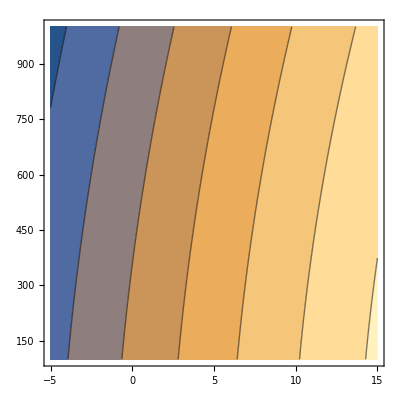

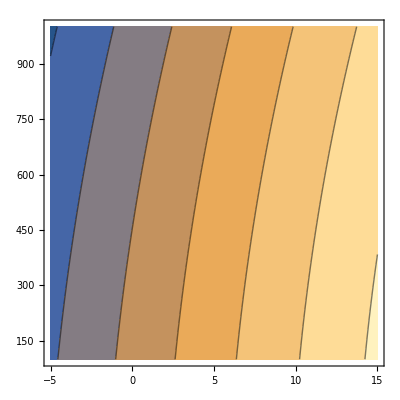

```mathematica
(*Contour plot quadratic form*)
ContourPlot[fittedSurf1[p,T],{p,-5,15},{T,100,1000}]
ContourPlot[fittedSurf2[p,T],{p,-5,15},{T,100,1000}]
```

```mathematica
(*Plot in 3D*)
p1=Plot3D[fittedSurf1[p,T],{p,-4,12},{T,100,2000},PlotStyle->{Red,Directive[Opacity[0.4]]}];
p2=ListPlot3D[cacSurf[[1]],PlotStyle->{Green,Directive[Opacity[0.4]]}];
p3=Plot3D[fittedSurf2[p,T],{p,-4,12},{T,100,2000},PlotStyle->{Orange,Directive[Opacity[0.4]]}];
p4=ListPlot3D[cacSurf[[2]],PlotStyle->{Blue,Directive[Opacity[0.4]]}];
```

```mathematica
(*Show plots*)
Show[{p1,p2}]
Show[{p3,p4}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Inspect equations*)
surf1=eqnForm/.fittedSurf1[[1]][[2]]
surf2=eqnForm/.fittedSurf2[[1]][[2]]
```

-941.488+0.0146882 p-0.0000964396 p^2-0.0000253548 T+3.77171×10^-7 p T-2.4741×10^-8 T^2

-941.483+0.0137978 p-0.0000543645 p^2-0.0000262425 T+3.44166×10^-7 p T-2.46611×10^-8 T^2

```mathematica
(*Solve intersections*)
surfDiff=surf1-surf2
intersection=Solve[surfDiff==0,{T,p}][[1]]
```

-0.00477935+0.00089033 p-0.0000420751 p^2+8.87745×10^-7 T+3.30044×10^-8 p T-7.98877×10^-11 T^2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{p→1.62708×10^-57 (6.50259×10^57+2.4105×10^53 T-2.06788×10^20 √(-1.4568×10^73+2.5969×10^71 T-1.54133×10^67 T^2))}

```mathematica
intersection[[1]][[2]]
```

1.62708×10^-57 (6.50259×10^57+2.4105×10^53 T-2.06788×10^20 √(-1.4568×10^73+2.5969×10^71 T-1.54133×10^67 T^2))

```mathematica
(*Plot the intersection - note it won't be value for this whole range*)
```

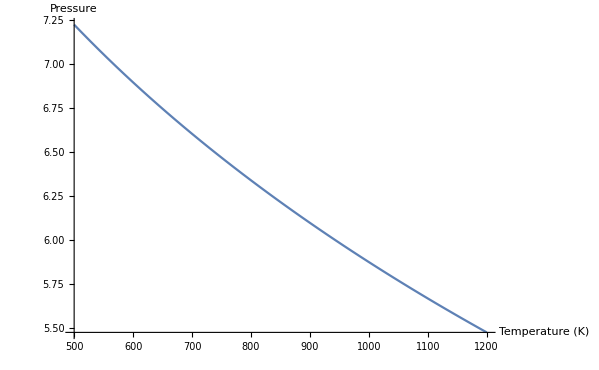

```mathematica
Plot[intersection[[1]][[2]],{T,500,1200},AxesLabel->{"Temperature (K)","Pressure"}]
```